```mathematica
Sll[M_]:=(1-M)/(1+M);
Srl[M_]:=2Sqrt[M]/(1+M);
Srr[M_]:=-Sll[M];
Slr[M_]:=Srl[M];
S2ll[M_,l_,b_,k_]:=Sll[M]+Exp[2I k l b]Srl[M] Sll[M] Slr[M]/(1-Exp[2I k l b]Sll[M] Srr[M]);
S2rl[M_,l_,b_,k_]:=Exp[I k l b] Srl[M]^2/(1-Exp[2I k l b]Sll[M] Srr[M] );
S2rr[M_,l_,b_,k_]:=Srr[M]+Exp[2I k l b]Slr[M] Srr[M] Srl[M]/(1-Exp[2I k l b]Srr[M] Sll[M]);
S2lr[M_,l_,b_,k_]:=Exp[I k l b] Slr[M]^2/(1-Exp[2I k l b]Srr[M] Sll[M] );
Manipulate[
Plot[{
Abs[S2ll[M,l,b,k]]^2,
Abs[S2rl[M,l,b,k]]^2,
Abs[S2ll[M,l,b,k]]^2+Abs[S2rl[M,l,b,k]]^2
},{k,0,2Pi},PlotRange->{0,1.1}],
{M,2,10},{{l,1},0,10},{{b,0.5},0,1}]
```

```mathematica
S3ll[M_,l_,b_,k_]:=S2ll[M,l,b,k]+Exp[2I k l b^2]S2rl[M,l,b,k] S2ll[M,l,b,k] S2lr[M,l,b,k]/(1-Exp[2I k l b^2]S2ll[M,l,b,k] S2rr[M,l,b,k]);
S3rl[M_,l_,b_,k_]:=Exp[I k l b^2] S2rl[M,l,b,k]^2/(1-Exp[2I k l b^2]S2ll[M,l,b,k] S2rr[M,l,b,k] );
Manipulate[
Plot[{
Abs[S3ll[m,l ,b,k]]^2,
Abs[S3ll[m,l ,b,k]]^2+Abs[S3rl[m,l ,b,k]]^2
},{k,0,10},PlotRange->{0,1}],
{m,2,10,1,Appearance->"Labeled"},
{{l,1},0,5,Appearance->"Labeled"},
{{b,0.5},0,1,Appearance->"Labeled"}]
```

```mathematica
SNll[1,M_,l_,b_,k_]:=(1-M)/(1+M);
SNrl[1,M_,l_,b_,k_]:=2Sqrt[M]/(1+M);
SNrr[1,M_,l_,b_,k_]:=-SNll[1,M,l,b,k];
SNlr[1,M_,l_,b_,k_]:=SNrl[1,M,l,b,k];

SNll[N_,M_,l_,b_,k_]:=SNll[N-1,M,l,b,k]+Exp[2I k l b^(N-1)]SNrl[N-1,M,l,b,k] SNll[N-1,M,l,b,k] SNlr[N-1,M,l,b,k]/(1-Exp[2I k l b^(N-1)]SNll[N-1,M,l,b,k] SNrr[N-1,M,l,b,k]);
SNrl[N_,M_,l_,b_,k_]:=Exp[I k l b^(N-1)] SNrl[N-1,M,l,b,k]^2/(1-Exp[2I k l b^(N-1)]SNll[N-1,M,l,b,k] SNrr[N-1,M,l,b,k] );
SNrr[N_,M_,l_,b_,k_]:=-SNll[N,M,l,b,k];
SNlr[N_,M_,l_,b_,k_]:=SNrl[N,M,l,b,k];
```

```mathematica
Manipulate[
Plot[Abs[SNll[N,M,l ,b,k]]^2,{k,0,10},PlotRange->{0,1}],
{N,1,5,1,Appearance->"Labeled"},
{M,2,10,1,Appearance->"Labeled"},
{{l,1},0,10,Appearance->"Labeled"},
{{b,0.5},0,1,Appearance->"Labeled"}]
```

```mathematica
R[1,m_,l_,b_,k_]:=(1-m)/(1+m)
T[1,m_,l_,b_,k_]:=2Sqrt[m]/(1+m)
R[n_,m_,l_,b_,k_]:=R[n-1,m,l,b,k]*(1+Exp[2I k l b^(n-1)](R[n-1,m,l,b,k]^2+T[n-1,m,l,b,k]^2))/(1+Exp[2I k l b^(n-1)]R[n-1,m,l,b,k]^2)
T[n_,m_,l_,b_,k_]:=Exp[I k l b^(n-1)]T[n-1,m,l,b,k]^2/(1+Exp[2I k l b^(n-1)]R[n-1,m,l,b,k]^2)
Manipulate[
Plot[Abs[R[n,m,l ,b,k*Pi]]^2,{k,0,kmax},PlotRange->{0,1},AxesLabel->{"kπ","|R|^2"}],
{n,2,10,1,Appearance->"Labeled"},
{m,2,20,1,Appearance->"Labeled"},
{{l,1},0,10,Appearance->"Labeled"},
{{b,0.5},0,1,Appearance->"Labeled"},
{kmax,2,100,Appearance->"Labeled"}]
```

```mathematica
NIntegrate[Abs[R[6,2,1 ,0.5,k]]^2,{k,0,32Pi},WorkingPrecision->18,MaxRecursion->20]/32Pi
```

NIntegrate::precw: The precision of the argument function (1/9\ Abs[(1 + ⅇ^(0.  + 1.\ ⅈ)\ k)\ (1 + ⅇ^Times[« 2 »]\ (Times[« 3 »] + Times[« 3 »]))\ (« 1 »)\ (1 + ⅇ^« 1 »\ (« 1 »))\ (1 + ⅇ^Times[« 2 »]\ (Times[« 6 »] + Times[« 9 »]))/(1 + 1/9\ Power[« 2 »])\ « 3 »\ (1 + 1/9\ Power[« 2 »]\ Power[« 2 »]\ Power[« 2 »]\ Power[« 1 »]\ « 1 »\ Power[« 2 »]\ Power[« 2 »]\ Power[« 2 »]\ Power[« 2 »])]^2) is less than WorkingPrecision (18.).

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

5.3328930535687111

```mathematica
R[3,m,ℓ,β,k]//FullSimplify
```

-((1+ⅇ^(2 ⅈ k ℓ β)) (-1+m) (1+m) (ⅇ^(2 ⅈ k ℓ β) (-1+m)^2+ⅇ^(2 ⅈ k ℓ β^2) (-1+m)^2+(1+m)^2+ⅇ^(2 ⅈ k ℓ β (1+β)) (1+m)^2))/(ⅇ^(4 ⅈ k ℓ β) (-1+m)^4+(1+m)^4+2 ⅇ^(2 ⅈ k ℓ β) (-1+m^2)^2+ⅇ^(2 ⅈ k ℓ β^2) (-1+m^2)^2+2 ⅇ^(2 ⅈ k ℓ β (1+β)) (-1+m^2)^2+ⅇ^(2 ⅈ k ℓ β (2+β)) (-1+m^2)^2)

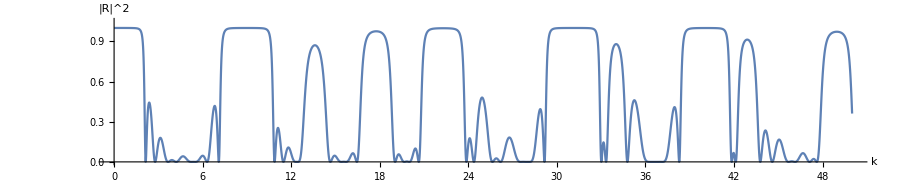

```mathematica
Plot[Abs[R[5,2,1,0.3,k]]^2,{k,0,50},PlotRange->{0,1.05},AspectRatio->0.2,AxesLabel->{k,"|R|^2"}]
```

```mathematica
ClearAll[m,bound];
```

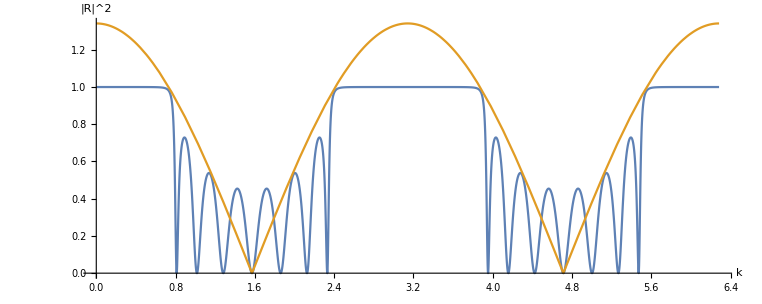

```mathematica
m=5;
bound=(Sqrt[m]+1/Sqrt[m])/2;
Plot[{Abs[R[4,m,1,1,k]]^2,bound Abs[Cos[k]]},{k,0,2 Pi},PlotRange->{0,bound},AspectRatio->0.4,AxesLabel->{k,"|R|^2"},GridLines->{{ArcCos[1/bound],Pi-ArcCos[1/bound],Pi+ArcCos[1/bound],2 Pi-ArcCos[1/bound]},{1,-1}}]
```

```mathematica
NIntegrate[Abs[R[5,6,1,1,k]]^2,{k,0,Pi},WorkingPrecision->20,MaxRecursion->20]/Pi
```

0.71428571428520788847

```mathematica
7/9//N
4/5//N
```

0.777778

0.8

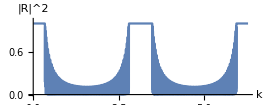

```mathematica
Plot[Abs[R[7,2,1,1,k]]^2,{k,0,2Pi},PlotRange->{0,1.05},AspectRatio->0.4,AxesLabel->{k,"|R|^2"},PlotPoints->100]
```